```mathematica
Do[
v=5;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];


Chi5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-5.txt",{Number,Number}];
Chit5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-5.txt",{Number,Number}];
Chi6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-6.txt",{Number,Number}];
Chit6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-6.txt",{Number,Number}];
Chi7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-7.txt",{Number,Number}];
Chit7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-7.txt",{Number,Number}];
Chi8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-8.txt",{Number,Number}];
Chit8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-8.txt",{Number,Number}];


Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];

Chii[v][l]=Table[{Chi5[[All,1]][[i]],(Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]])/4.},{i,1,Length[Chi5]}];
Chiit[v][l]=Table[{Chit5[[All,1]][[i]],(Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]])/4.},{i,1,Length[Chi5]}];

Ch4[v][l]=Join[Chi[v][l],Chii[v][l]];
Cht4[v][l]=Join[Chit[v][l],Chiit[v][l]];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

,{l,{2,5,10,20,40}}]
```

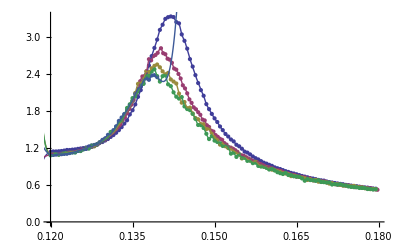

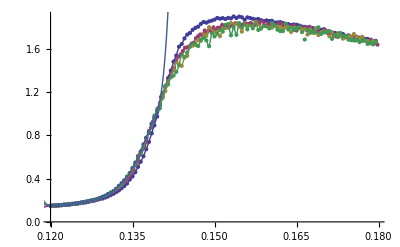

```mathematica
v=5;
pic1=ListPlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40]},PlotRange->Full];
pic2=Plot[{i4[v][2][i],i4[v][5][i],i4[v][10][i],i4[v][20][i],i4[v][40][i]},{i,0.11,0.16},PlotRange->Full];
pic3=ListPlot[{Cht4[v][2],Cht4[v][5],Cht4[v][10],Cht4[v][20],Cht4[v][40]},PlotRange->Full];
pic4=Plot[{it4[v][2][i],it4[v][5][i],it4[v][10][i],it4[v][20][i],it4[v][40][i]},{i,0.11,0.16},PlotRange->Full];
Show[{pic1,pic2}]
Show[{pic3,pic4}]
```

```mathematica
i4[v][2][0.12]
```

Interpolation[Ch4[5][2]][0.12]